Part 1: Initialization of Parameters

```mathematica
Needs["ComputerArithmetic`"];
echarge=1.60217646*10^-19; emass=9.10938188*10^-31;Plancks=6.626068*10^-34;CoulombConstant=8.98755179*10^-9;
```

```mathematica
(*Specify input parameter*)
chargeratio=0;(*strength of image charge (in units of e)*)
lam=Sqrt[150/4000]*10^-10;(*compute wavelength for electrons*)
lambda=10*10^-12;(*lam//global variable containing value of wavelength*)
eta1=.4;(*G1 open fraction*)
eta2=eta1;(*G2 open fraction*)
d=10^-7;(*period of grating*)

r0=-4.04;(*initial radius of wavefront curvature*)
el0=1*10^-6;(*50e-9// //initial coherence width*)
w0=30*10^-6;(*2e-6//1e-6// //initial beam width*)

G1z=1*10^-6;(*//5e-3*)
G2z=1;(*G1_z+4*d^2/lambda//-.1e-3//G2_x=d/2//initial lateral offset of G2*)
G2x=d/2;
theta=0;(*//.05//twist between gratings,in degrees*)
```

### Part 2: Load Fourier Components

```mathematica
energy=1.5*10^-18/(lambda^2);width=eta2*d;thick=140*10^-9;wedgeangle=0;tilt=0;
ReT=Transpose[{-20+(#-1)&/@Range[41],ConstantArray[0,41]}];ImT=ReT;
res=1000;
eta=width/d;
vel=Sqrt[2*energy*e_charge/e_mass];
alpha=wedgeangle*Pi/180;
beta=tilt*Pi/180;
xmin=If[beta≥0,-((width Cos[beta])/2)+width/res,If[Abs[beta]≤alpha,-((width Cos[beta])/2)+width/res,-((width Cos[beta])/2)+width/res-thick*(Tan[alpha]-Tan[beta])]];
xmax=If[beta≥0,If[beta≤alpha,(width Cos[beta])/2-width/res,(width Cos[beta])/2-width/res+thick*(Tan[alpha]-Tan[beta])],(width Cos[beta])/2-width/res];
x2pnt[arr__,n_]:=Position[arr[[All,1]],n][[1]][[1]](*return index where n occurs in the index of ImT or ReT*)
For[n=-20,n≤20,n++,For[ex=xmin,ex<xmax,ex+=width/res,fc=2 Pi n ex/d;
ph=-width*thick*chargeratio*echarge^2*(2*Pi*CoulombConstant/Plancks)/(vel*(.25*width^2-ex^2));
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[ph+fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[ph+fc];]];
ReT[[All,2]]/=res;ImT[[All,2]]/=res;
```

#### Testing:

```mathematica
ReT;
```

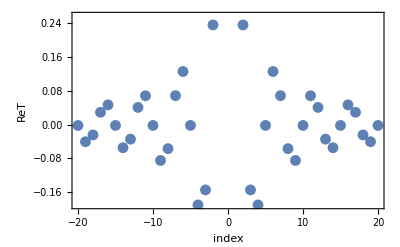

```mathematica
ListPlot[ReT,Frame->True,FrameLabel->{"index","ReT"}]
```

```mathematica
ImT;
```

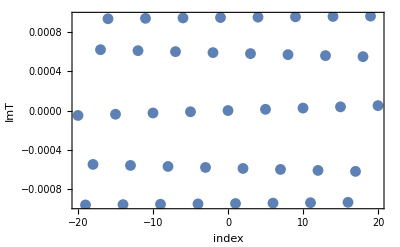

```mathematica
ListPlot[ImT,Frame->True,FrameLabel->{"index","ImT"}]
```

### Part 3: Set spatial limits of simulation and initialize waves containg simulation outputs

```mathematica
(*Specify input array*)
zstart=-.1;(*//-2e-3//-5e-3//-.8e-3//1e-6*)
zend=2.1;(*//6e-3//40e-3//100e-3//7//6*(d^2)/lambda//xstart=-200e-6//e-8e-6//-1.5e-3*)
xstart=-200*10^-6;(*//e-8e-6//-1.5e-3*)
xend=200*10^-6;(*//8e-6//1.5e-3*)
ystart=-0.11*10^-3;
yend=0.11*10^-3;

xpnts=300;(*resolution in the x direction*)
ypnts=300;(*resolution in the y direction*)
zpnts=300;(*resolution in the z direction*)

zres=(zend-zstart)/zpnts;(*step resolution used in computation*)
```

```mathematica
(*Initialize the arrays used for calculation*)
(*izx=Partition[Flatten[Riffle[xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Prepend[Range[xpnts],0],Prepend[ConstantArray[ConstantArray[0,zpnts],xpnts],zstart+(#-1) ((zend-zstart)/(zpnts-1))&/@Range[zpnts]]]],xpnts+1];*)
ixy=Partition[Flatten[Riffle[xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Prepend[Range[xpnts],0],Prepend[ConstantArray[ConstantArray[0,ypnts],xpnts],ystart+(#-1) ((yend-ystart)/(ypnts-1))&/@Range[ypnts]]]],xpnts+1];
fmap=ConstantArray[ConstantArray[0,zpnts],Ceiling[xpnts/2]];
ix=Transpose[{xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Range[xpnts],ConstantArray[0,xpnts]}];
g1=Transpose[{xstart+(#-1) ((xend-xstart)/(2 xpnts-1))&/@Range[xpnts*2],ConstantArray[NaN,xpnts*2]}];
g2=g1;
vis=Transpose[{(zstart-G1z)+(#-1) ((zend-zstart)/(zpnts-1))&/@Range[zpnts],ConstantArray[0,zpnts]}];

(*izx=Prepend[
Prepend[ConstantArray[ConstantArray[0,zpnts],xpnts],
xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Range[xpnts]],
zstart+(#-1) ((zend-zstart)/(zpnts-1))&/@Range[zpnts]];*)
izx=ConstantArray[ConstantArray[0,zpnts],xpnts];
```

### Part 4: Plotting the gratings g1 and g2

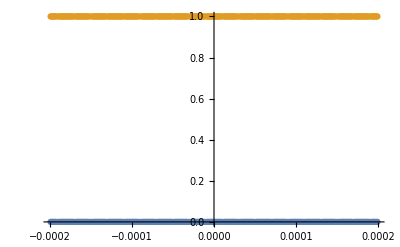

```mathematica
(*
g1=NaN
g2=NaN
if(1)//plot gratings
if((G1_z≥zstart)&&(G1_z≤zend))
g1=((x>d*round(x/d)-d*eta1/2)&&(x<d*round(x/d)+d*eta1/2))?NaN:G1_z
endif
if((G2_z≥zstart)&&(G2_z≤zend))
g2=((x-G2_x>d*round(x/d)-d*eta2/2)&&(x-G2_x<d*round(x/d)+d*eta2/2))?NaN:G2_z
endif
endif*)
f1[x_]:=If[((x>d*Round[x/d]-d*eta1/2)&&(x<d*Round[x/d]+d*eta1/2)),NaN,G1z];
g1[[All,2]]=Map[f1,g1[[All,1]]];
f2[x_]:=If[((x>d*Round[x/d]-d*eta2/2)&&(x<d*Round[x/d]+d*eta2/2)),NaN,G2z];
g2[[All,2]]=Map[f2,g2[[All,1]]];
ListPlot[{g1,g2}]
```

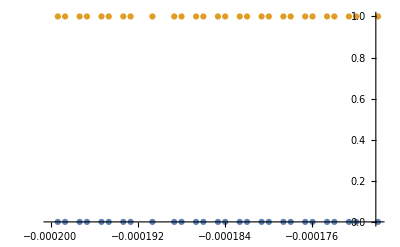

```mathematica
ListPlot[{g1,g2},PlotRange->{{-200*10^-6,-170*10^-6},{-5*10^-6,1}}](*Zoomed in version*)
```

### Part 5: Calculating GSM parameter at first grating

```mathematica
w[z_,r0_,el0_,w0_]:=el0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(el0^2 w0^2)];(*GSM beam width*)
zp[z_,v_]:= (v z)/(v+z);(*Magnification factor due to wavefront curvature*)
el[z_,r0_,el0_,w0_]:=el0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(el0^2 w0^2)];(*GSM coherence length*)
v[z_,r0_,el0_,w0_]:=z/(1-zp[z,r0]/(z*(1+lambda^2*zp[z,r0]^2/(el0^2*w0^2))));(*radius of wavefront curvature*)
r1=v[G1z,r0,el0,w0];
el1=el[G1z,r0,el0,w0];
w1=w[G1z,r0,el0,w0];
```

### Part 6: gp0

```mathematica
gp0[z01_,r0_,el0_,w0_]:=Block[
{w1=w[z01,r0,el0,w0],
ix=Transpose[{xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Range[xpnts],ConstantArray[0,xpnts]}]
},

ix[[All,2]]=Map[Exp[-Pi*(#/w1)^2]&,ix[[All,1]]];

Return[ix];
];
```

#### Testing:

```mathematica
gp0[zstart+zres*1,r0,el0,w0];
```

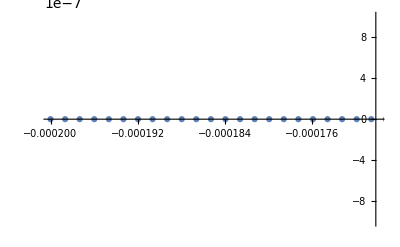

```mathematica
ListPlot[%,PlotRange->{{-200*10^-6,-170*10^-6},{-10^-6,10^-6}}](*Zoomed in*)
```

### Part 7: gp1

```mathematica
gp1[z12_,r1_,el1_,w1_]:=Block[
{el2=el[z12,r1,el1,w1],
w2=w[z12,r1,el1,w1],
r2=v[z12,r1,el1,w1],
(*ix initialized to zero,put definition of ix again*)
ix=Transpose[{xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Range[xpnts],ConstantArray[0,xpnts]}],
cutoff=1*10^-3,
lim=5,
dn=0,dm=0,coef=1},
(*Print[el2]; (*for debugging*)*)
Do[
dn=n-m;
dm=(m+n)/2;

If[ False,(*If true, ignore effect of image charge*)
coef=Sinc[eta1*Pi*n]*Sinc[eta1*Pi*m]*eta1^2,coef=ReT[[x2pnt[ReT,n]]][[2]]*ReT[[x2pnt[ReT,m]]][[2]]+ImT[[x2pnt[ReT,n]]][[2]]*ImT[[x2pnt[ReT,m]]][[2]]];
coef*=Exp[-Pi*(dn*lambda*z12/(d*el2))^2];
(*Print[coef]; debugging*)
If[coef≥cutoff,(*ix[[All,2]]+=coef*Exp[-Pi*((x-dm*lambda*z12/d)/w2)^2]]*Cos[2*Pi*(dn/d)*(x-dm*lambda*z12/d)*(1-z12/r2)];*)ix[[All,2]]=ix[[All,2]]+Map[(coef*Exp[-Pi*((#[[1]]-dm*lambda*z12/d)/w2)^2]*Cos[2*Pi*(dn/d)*(#[[1]]-dm*lambda*z12/d)*(1-z12/r2)])&,ix];
],

{n,-lim,lim,1},{m,-lim,lim,1}];
Return[ix];
];
```

#### Testing:

```mathematica
gp1[zstart-G1z+zres*100,r1,el1,w1];
```

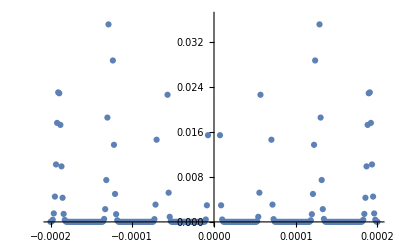

```mathematica
ListPlot[%]
```

### Part 8: gp2

```mathematica
gp2[z12_,z23_,mytheta_,el1x_,w1x_,r1x_,el1y_,w1y_,r1y_,G2x_]:=Block[
{theta=Pi*mytheta/180,
d1=d,
d2=d,
z13=z12+z23,
el3x=el[z12+z23,r1x,el1x,w1x],
w3x=w[z12+z23,r1x,el1x,w1x],
v3x=v[z12+z23,r1x,el1x,w1x],
el3y=el[z12+z23,r1y,el1y,w1y],
w3y=w[z12+z23,r1y,el1y,w1y],
v3y=v[z12+z23,r1y,el1y,w1y],
ix=Transpose[{xstart+(#-1) ((xend-xstart)/(xpnts-1))&/@Range[xpnts],ConstantArray[0,xpnts]}],
phix=ix,phi=0,
cutoff=1*10^-3, 
lim=5(*5*),
coef=0,dn=0,dm=0,m=0,n=0,a=0,b=0,c=0,d=0},

Do[
dn=n1-n2;
n=(n1+n2)/2;
dm=m1-m2;
m=(m1+m2)/2;
a = x2pnt[ReT,m1];
b=x2pnt[ReT,m2];
c=x2pnt[ReT,n1];
d=x2pnt[ReT,n2];
If[False,
{coef=Sinc[eta1*Pi*m1]+0ⅈ,
coef*=Sinc[eta1*Pi*m2+0ⅈ]},
{coef=ReT[[a]][[2]]+ImT[[a]][[2]]ⅈ,
coef*=ReT[[b]][[2]]-ImT[[b]][[2]]ⅈ}];
coef*=ReT[[c]][[2]]+ImT[[c]][[2]]ⅈ;
coef*=ReT[[d]][[2]]+ImT[[d]][[2]]ⅈ;
(*Accounting for twist dependence of visibility*)
coef*=Exp[-Pi*(dn*Sin[theta]*lambda*z23/(d2*el3y))^2];
coef*=Exp[-Pi*(lambda*z23*(dn*Cos[theta]+dm*z13/z23)/(d1*el3x))^2];
(*Print[ix[[All,1]]];
ix[[All,2]]+=Map[(Re[coef]*Cos[#[[2]]]-Im[coef]*Sin[#[[2]]])*Exp[-Pi*((#[[1]]-(lambda*z23/d1)*(n*Cos[theta]+m*z13/z23))/w3x)^2]&,phi];
Print[ix]*)
If[Re[coef]≥cutoff ||Im[coef]≥cutoff,
{
phi=dn*n*(1-z23/v3x)*Cos[theta]^2+dn*n*(1-z23/v3y)*Sin[theta]^2+dn*m*(1-z13/v3x)*Cos[theta];phi+=dm*n*(1-z13/v3x)*Cos[theta]+dm*m*(z13/z23)*(1-z13/v3x);phi*=2*Pi*lambda*z23/(d1^2);phi-=2*Pi*dn*G2x/d2;phix[[All,2]]=Map[(phi-(2*Pi*#/d2)*(dn*Cos[theta]*(1-z23/v3x)+dm*(1-z13/v3x))&),phix[[All,1]]];

ix[[All,2]]+=Map[(Re[coef]*Cos[#[[2]]]-Im[coef]*Sin[#[[2]]])*Exp[-Pi*((#[[1]]-(lambda*z23/d1)*(n*Cos[theta]+m*z13/z23))/w3x)^2]&,phix]
}
]
,

{m1,-lim,lim,1},{m2,-lim,lim,1},{n1,-lim,lim,1},{n2,-lim,lim,1}];

Return[ix]];
```

#### Testing:

```mathematica
gp2[G2z-G1z,zstart+0*zres,theta,el1,w1,r1,el1,w1,r1,G2x];
```

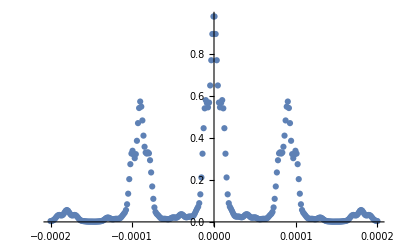

```mathematica
ListPlot[%]
```

### Part 9: Compute intensity along z axis

```mathematica
Do[
zloc=zstart+i*zres;
If[zloc>G2z,
{ix=gp2[G2z-G1z,zloc-G2z,theta,el1,w1,r1,el1,w1,r1,G2x];}
,
If[zloc>G1z,
{ix=gp1[zloc-G1z,r1,el1,w1];}
,
{ix=gp0[zloc,r0,el0,w0];}
]
];
filter[x_]:=If[x<0,0,x];
ix[[All,2]]=Map[filter,ix[[All,2]]];
ix[[All,2]]/=Max[ix[[All,2]]];
izx[[All,i+1]]=ix[[All,2]];
,
{i,0,zpnts-1,1}]
```

```mathematica
izx
```

{{1.23585900362563×10^-51915,1.1778184117767×10^-52107,3.57834680384507×10^-52300,3.50394406168853×10^-52493,1.11841312493233×10^-52686,1.1771791787779×10^-52880,288,0.460778,0.378052,0.32623,0.196508,0.308078,0.293111},{1},296,{1},{1}}
 |  |  |  |

```mathematica
Export["out.dat",izx]
```

out.dat

```mathematica
Image[Transpose[N[izx,{15,10}]]]
```

-Graphics-

```mathematica
ImageRotate[%103,Left]
```

```mathematica
Export["test.pdf",-Graphics-]
```

test.pdf